```mathematica
Clear["Global`*"] (*with flow*)
Q = {{1-μ,μ,0},{0,1,0},{0,0 ,1}}; 
Q//MatrixForm
```

(1-μ | μ | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
P = {{1,0,1+w},{1+w,1,0},{0,1+w,1}};
P//MatrixForm
```

(1 | 0 | 1+w
1+w | 1 | 0
0 | 1+w | 1)

```mathematica
Frequency = {x,y,z};
Fitness = P.Frequency;
ϕ = Frequency.Fitness //FullSimplify;
RHSX = x*Q[[1,1]]*Fitness[[1]] + y*Q[[2,1]]*Fitness[[2]] + z*Q[[3,1]]*Fitness[[3]]-x*ϕ;
RX = RHSX /. {z -> 1-x-y} //FullSimplify;
RHSY = x*Q[[1,2]]*Fitness[[1]] + y*Q[[2,2]]*Fitness[[2]] + z*Q[[3,2]]*Fitness[[3]]-y*ϕ;
RY = RHSY /. {z -> 1-x-y} //FullSimplify;
F = {RX,RY}
FPrules =Solve[RX==0 && RY==0,{x,y}]//FullSimplify;
FPS = {x,y}/.FPrules;
```

{x (x-x^2-x y-y^2+(-1+y) μ+w (x^2+x (-2+y+μ)+(-1+y) (-1+y+μ))),(2+w (-1+x)-x) y^2+(-1+w) y^3+x (1+w-w x) μ+y (-1+x (2+(-1+w) x-(1+w) μ))}

```mathematica
Assuming[{w>0},Simplify[Series[FPS,{α,0,1}]]]
```

{{0,0},{0,1},{0,1/(1-w)},{(-2+w+μ+√(-4 μ+(w+μ)^2))/(2 (-1+w)),-(-w+μ+√(-4 μ+(w+μ)^2))/(2 (-1+w))},{(-2+w+μ-√(-4 μ+(w+μ)^2))/(2 (-1+w)),(w-μ+√(-4 μ+(w+μ)^2))/(2 (-1+w))},{1/(2 (-1+w^3) (3+(-3+μ) μ))(-1+w^2 (3+2 (-2+μ) μ)+w^3 (4+μ (-5+2 μ))-√((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2)+μ (-2+μ+√((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2))+w (3-2 √((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2)+μ (-4+μ+√((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2)))),-(1-w^3-3 μ-2 w μ+w^2 μ+w^3 μ+2 μ^2+w μ^2+(1+w (-1+μ)) √((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2))/(2 (-1+w^3) (3+(-3+μ) μ))},{1/(2 (-1+w^3) (3+(-3+μ) μ))(-1+μ^2+w^2 (3+2 (-2+μ) μ)+w^3 (4+μ (-5+2 μ))+√((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2)-μ (2+√((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2))+w (3+μ^2+2 √((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2)-μ (4+√((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2)))),(-1+w^3+3 μ+2 w μ-w^2 μ-w^3 μ-2 μ^2-w μ^2+(1+w (-1+μ)) √((1+w+w^2)^2-6 (1+w+w^2) μ+(μ+2 w μ)^2))/(2 (-1+w^3) (3+(-3+μ) μ))}}

```mathematica
G = F/. {x -> u-(v/3^{1/2}),y -> 2*v/3^{1/2}};
xp = Part[G,1];
yp = Part[G,2];
vp = 3^{1/2}*yp/2;
up = xp + yp/2;
H = {up,vp}//FullSimplify;
F = H/. {u->x+1/2, v-> y+1/(2*3^(1/2))}// FullSimplify;
X = {x,y};
F = Flatten[F]
```

{1/18 (18 (-1+w) x^3-3 (1+w) (√3-3 y) y+9 x^2 (-1+w (-1+μ))+(2+w) (-1+2 √3 y-3 y^2) μ+3 x (1-w+6 (-1+w) y^2-2 μ+2 √3 y (-1+w+μ))),1/18 (18 (-1+w) y^3+3 √3 y^2 (1+w (-1+μ)+2 μ)+√3 (3 x (1+w+(-1+w) x)+(2+w+6 x-9 w x^2) μ)-3 y (-1+w-6 w x (1+x)+4 μ+2 w μ+6 x (-1+x+μ)))}

```mathematica
FPnew = {(2x+y-1)/2,(3y-1)/(2*3^(1/2))}/.FPrules //FullSimplify;
```

```mathematica
F/.{x->FPnew[[1]][[1]],y->FPnew[[1]][[2]]}//Simplify;
F/.{x->FPnew[[2]][[1]],y->FPnew[[2]][[2]]}//Simplify;
F/.{x->FPnew[[3]][[1]],y->FPnew[[3]][[2]]}//Simplify;
F/.{x->FPnew[[4]][[1]],y->FPnew[[4]][[2]]}//Simplify;
F/.{x->FPnew[[5]][[1]],y->FPnew[[5]][[2]]}//Simplify;
F/.{x->FPnew[[6]][[1]],y->FPnew[[6]][[2]]}//Simplify;
F/.{x->FPnew[[7]][[1]],y->FPnew[[7]][[2]]}//Simplify;
```

```mathematica
(*Given an α want to find Hopf in w*)
```

```mathematica
(*############FP1 -(0,0)###############*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[1]][[1]],y->FPnew[[1]][[2]]};
Jacc //FullSimplify// MatrixForm
```

(w-1/2 (1+w) μ | ((1+w) (-2+μ))/(2 √3)
1/2 √3 (1+w) μ | -1-1/2 (1+w) μ)

```mathematica
Eigenvalues[{{w-1/2 (1+w) α,((1+w) (-2+α))/(2 √3)},{1/2 √3 (1+w) α,-1-1/2 (1+w) α}}] (*Bifurcation at α=w/(1+w). α<w/(1+w)->saddle. α>w/(1+w)->Stable Node.
collides with FP7*)
```

{-1,w-α-w α}

```mathematica
(*############FP2 -(0,1)###############*)
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[2]][[1]],y->FPnew[[2]][[2]]};
Jacc //FullSimplify// MatrixForm
```

(1/2 (-1+w) | (1+w)/(2 √3)
1/2 √3 (1+w) | 1/2 (-1+w))

```mathematica
Eigenvalues[{{1/2 (-1+w),(1+w)/(2 √3)},{1/2 √3 (1+w),1/2 (-1+w)}}](*Saddle for w>0*)
```

{-1,w}

```mathematica
(*############FP3- (0,1/(1-w)) does not exist###############*)
(*############FP4- does not exist ###############*)
Manipulate[Plot[{(-2+w+α+√(-4 α+(w+α)^2))/(2 (-1+w)),-(-w+α+√(-4 α+(w+α)^2))/(2 (-1+w)),0,1},{w,0,2}],{α,0,1}];
(*############FP5- does not exist ###############*)
Manipulate[Plot[{(-2+w+α-√(-4 α+(w+α)^2))/(2 (-1+w)),(w-α+√(-4 α+(w+α)^2))/(2 (-1+w)),0,1},{w,0,2}],{α,0,1}];
```

```mathematica
(*############FP6- near(1/3,1/3)-when does it exist? ###############*)
XP = Part[F,1];
YP = Part[F,2];
```

```mathematica
Jacc = D[F,{X}]/.{x->FPnew[[6]][[1]],y->FPnew[[6]][[2]]};
Jacc //FullSimplify// MatrixForm;
```

```mathematica
Jacc ={{1/18 (1/(2 (-1+w^3) (3+(-3+α) α))9 (-1+w (-1+α)) (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))+(27 (-1+w) (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))^2)/(8 (-1+w^3)^2 (3+(-3+α) α)^2)+3 (1-w-2 α+(-1+w+α) (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α)))+1/2 (-1+w) (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α)))^2)),1/18 (3/2 √3 (1+w) (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α)))+(2+w) α (2 √3-√3 (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α))))-3 (1+w) (√3-1/2 √3 (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α))))+1/(4 (-1+w^3) (3+(-3+α) α))3 (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))) (2 √3 (-1+w+α)+2 √3 (-1+w) (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α)))))},{1/18 (-1/2 √3 (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α))) (1/(2 (-1+w^3) (3+(-3+α) α))3 (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))-1/(2 (-1+w^3) (3+(-3+α) α))3 w (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))-6 w (1+1/(4 (-1+w^3) (3+(-3+α) α))(3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))))+6 (-1+α+1/(4 (-1+w^3) (3+(-3+α) α))(3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))))+√3 (1/(4 (-1+w^3) (3+(-3+α) α))3 (-1+w) (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))+3 (1+w+1/(4 (-1+w^3) (3+(-3+α) α))(-1+w) (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))))+α (6-1/(2 (-1+w^3) (3+(-3+α) α))9 w (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))))),1/18 (3 (1+w (-1+α)+2 α) (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α)))+9/2 (-1+w) (-1-(3 (1-w^3-3 α-2 w α+w^2 α+w^3 α+2 α^2+w α^2+(1+w (-1+α)) √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))/(2 (-1+w^3) (3+(-3+α) α)))^2-3 (-1+w+4 α+2 w α-1/(2 (-1+w^3) (3+(-3+α) α))3 w (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))) (1+1/(4 (-1+w^3) (3+(-3+α) α))(3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))))+1/(2 (-1+w^3) (3+(-3+α) α))3 (3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))) (-1+α+1/(4 (-1+w^3) (3+(-3+α) α))(3-7 α+w^3 (-1+α) (-3+2 α)+w^2 (6+α (-9+4 α))-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+2 α (α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+w (6-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-6+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))))))}};
```

```mathematica
traceFP6 =Tr[%47]//FullSimplify;
determinantFP6 =Det[%47]//FullSimplify;
```

```mathematica
Manipulate[ParametricPlot[{{1/(2 (-1+w^3)^2 (3+(-3+α) α)^2)(1+w^8 (-1+α)^2+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+w^7 (10+α (-19-2 (-6+α) α))+w^6 (28+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-57-2 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (48+4 (-5+α) α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))-α (12-9 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-42+17 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (37-8 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-11+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))))+w^2 (28-18 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-173+62 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (307-71 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-242+35 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (85-10 α-6 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))))+w (10-9 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-82+44 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (162-49 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-121+20 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (40-5 α-3 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))))+w^4 (61-18 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-223+37 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (330-32 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-255+13 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (101-16 α-2 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))))+w^5 (52-9 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-149+19 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (196-19 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-2 α (-28+4 α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+5 (-29+2 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))))+w^3 (52-29 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-255+74 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (414-74 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-312+31 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)-2 α (-54+7 α+2 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))))),1/(2 (-1+w^3) (3+(-3+α) α))(2+w^4 (2+α (-3+2 α))-4 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+w^3 (10+α (-16+(11-2 α) α))-α (8-4 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-5+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))+w^2 (-4 (-3+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+α ((13-2 α) α+3 (-8+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))-w (-10+4 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (21-5 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-11+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))))},{α,Sqrt[4α]},{α,-Sqrt[4α]}},{α,0,1},AspectRatio->1],{w,1.01,4}]
```

```mathematica
HopfCondition1 =(Eigenvalues[Jacc][[1]]+ Eigenvalues[Jacc][[2]])//FullSimplify; (*need zero for hopf*)
HopfCondition2 =(Eigenvalues[Jacc][[1]]* Eigenvalues[Jacc][[2]])//FullSimplify; (*need positive for hopf*)
```

```mathematica
Assuming[{1/3 (-2+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3))<w},FullSimplify[HopfCondition2/.{α->w/(1+w)}]]//FullSimplify
```

```mathematica
Plot[w/.NSolve[HopfCondition2==0&&w>0,w],{α,0,1}]
```

```mathematica
Solve[HopfCondition2==0]
```

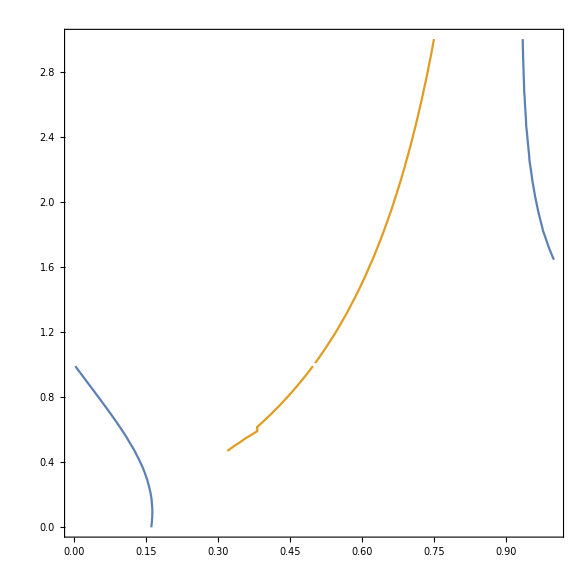

```mathematica
ContourPlot[{HopfCondition1==0,HopfCondition2==0},{α,0,1},{w,0,3}]
```

```mathematica
ω = (1+21 α+w (4+w) (1+3 α))/(6 √3);
f = XP +ω*y //FullSimplify;
g = YP -ω*x //FullSimplify;
anearly = ((D[f,{x,3}]+ D[f,{x,1},{y,2}]+ D[g,{x,2},{y,1}]+D[g,{y,3}]) + (1/ω)*(D[f,x,y]*(D[f,{x,2}]+D[f,{y,2}])-D[g,x,y]*(D[g,{x,2}]+D[g,{y,2}]) - D[f,{x,2}]*D[g,{x,2}]+D[f,{y,2}]*D[g,{y,2}]))/16 //FullSimplify;
x = 0;
y = 0;

a = anearly//FullSimplify;
a
```

```mathematica
(*############FP7- near(0,0) ###############*)
```

```mathematica
Manipulate[ParametricPlot[{{, },{α,Sqrt[4α]},{α,-Sqrt[4α]}},{α,0,1},PlotRange->{{-.5,.4},{-3,.6}},AspectRatio->1],{w,1.01,5}]
```

```mathematica
XP = Part[F,1];
YP = Part[F,2];
Jacc = D[F,{X}]/.{x->FPnew[[7]][[1]],y->FPnew[[7]][[2]]};
Jacc //FullSimplify// MatrixForm
```

$Aborted

```mathematica
traceFP7 =Tr[Jacc]//FullSimplify;
determinantFP7 =Det[Jacc]//FullSimplify;
```

```mathematica
(*Vector Field*)
Manipulate[StreamPlot[{x (x-x^2-x y-y^2+(-1+y) α+w (x^2+x (-2+y+α)+(-1+y) (-1+y+α))),(2+w (-1+x)-x) y^2+(-1+w) y^3+x (1+w-w x) α+y (-1+x (2+(-1+w) x-(1+w) α))},{x,0,1},{y,0,1},RegionFunction->Function[{x,y,vx,vy,n},x +y<1]],{α,0,.7},{w,0,.8}]
Clear[α,w]
```

```mathematica
(*It appears FP6 and FP7 collide and the new FP continues on to collide with FP at (0,0)
So maybe Hopf at FP6 then collide with FP7, does limit cycle collide with FP6 first?


FP6 collides with FP7 at α=(3+3 w (1+w)-2 √(-(-2+w+w^2) (1+w+w^2)^2))/(1+2 w)^2, which is real for 0<w<1. FP7 doesn't exist for w>1.

But, For α>1-(2/(3 (-9+√93)))^(1/3)+(1/2 (-9+√93))^(1/3)/3^(2/3) - FP7 Does not exist. So the maximum α for which we could have collision is 1-(2/(3 (-9+√93)))^(1/3)+(1/2 (-9+√93))^(1/3)/3^(2/3). This corresponds to a collision at w=1/3 (-2+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3)),
when FP6 and FP7 collide with FP1 simultaneously.

*)
```

```mathematica
(*Collision Location*)
{FPS[[7]][[1]],FPS[[7]][[2]]}/.{α->(3+3 w (1+w)-2 √(-(-2+w+w^2) (1+w+w^2)^2))/(1+2 w)^2}//FullSimplify;
```

```mathematica
1/3 (-2+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3))
```

1/3 (-2+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3))

```mathematica
N[1/3 (-2+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3))]
```

0.465571

```mathematica
HopfCondition1
```

```mathematica
HopfCondition1=1/(2 (-1+w^3) (3+(-3+α) α))(2+w^4 (2+α (-3+2 α))-4 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+w^3 (10+α (-16+(11-2 α) α))-α (8-4 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-5+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))+w^2 (-4 (-3+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))+α ((13-2 α) α+3 (-8+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2))))-w (-10+4 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (21-5 √((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)+α (-11+α+√((1+w+w^2)^2-6 (1+w+w^2) α+(α+2 w α)^2)))));
```

```mathematica
(*Bifurcation Diagram*)
(*p1 =Plot[(3+3 w (1+w)-2 √(-(-2+w+w^2) (1+w+w^2)^2))/(1+2 w)^2,{w,0,1/3 (-2+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3))},PlotRange->{{0,5},{0,1}},AspectRatio->1];*)
p1 =Plot[{(3+3 w (1+w)-2 √(-(-2+w+w^2) (1+w+w^2)^2))/(1+2 w)^2},{w,0,1/3 (-2+(29/2-(3 √93)/2)^(1/3)+(1/2 (29+3 √93))^(1/3))},PlotRange->{{0,1},{0,1/2}},AspectRatio->1,PlotStyle->{Red}];
p2 =ContourPlot[{α==w/(1+w)},{w,0,1},{α,0,1/2},PlotRange->{{0,2},{0,1}},AspectRatio->1,ContourStyle->{Blue}];
p3 =ContourPlot[{HopfCondition1==0},{w,0,1},{α,0,1/1},PlotRange->{{0,1},{0,1}},AspectRatio->1,ContourStyle->{Green}];
Frame->True,FrameLabel->{w,μ},LabelStyle->Directive[Black,Large]
p4 =ListPlot[HCcurve,Joined->True,PlotRange->{{0,1},{0,1/2}},AspectRatio->1, PlotStyle->Orange];
```

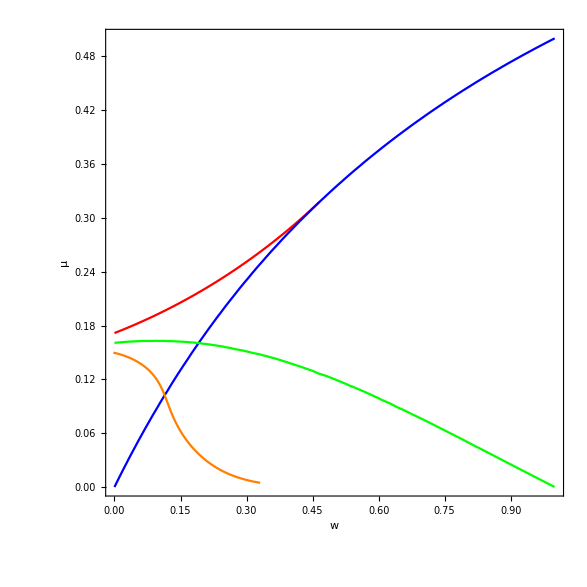

```mathematica
Show[p1,p2,p3,p4,Frame->True,FrameLabel->{w,μ},LabelStyle->Directive[Black,Large]]
```

```mathematica
(*Red curve - Saddle node curve. Blue Curve is transcritical! Green Curve is hopf.
Orange is line of homoclinic bifurcations, that may kill the limit cycle before it dissapears in the hopf.

Not a cusp point. It is a SN-T point, see Hoti and van veen for unfolding (fig.1)
located at the origin with a zero eigenvalue and 3 fixed points nearby.
*)
```

```mathematica
(*BOGDANOV-TAKENS point -> hopf and SN curnve intersect. Implies existence of Homoclinic curve.*)
```

```mathematica
waxis={-0.00245978325213986,
0.00432627871945352,
0.0109145067063843,
0.0172774411463479,
0.0234442117850389,
0.0294161811113473,
0.0351987110110196,
0.0407864260127586,
0.0461787705547473,
0.0513460370438386,
0.0563147201357849,
0.0610829402836435,
0.0656264474544605,
0.0699645576222919,
0.0740953788084479,
0.0779947220504707,
0.0816853242098847,
0.0851678654012779,
0.0884388566482569,
0.0915071432585202,
0.0943782338501660,
0.0970626455631456,
0.0995652565511886,
0.101897259834585,
0.104049127092769,
0.106059718099925,
0.107942890798857,
0.109730343487267,
0.111414394074938,
0.113008762251263,
0.114509175504263,
0.115949380004025,
0.117339647605939,
0.118676579202138,
0.119979541645957,
0.121255897334071,
0.122520408343382,
0.123769704537392,
0.125008861245115,
0.126247926442652,
0.127483829299962,
0.128719969569451,
0.129957667877835,
0.131201520620460,
0.132453870147827,
0.133737272465690,
0.135033204125153,
0.136343275188610,
0.137674677872126,
0.139021752378445,
0.140385578908611,
0.141774673079183,
0.143181614881107,
0.144607181128093,
0.146053392242590,
0.147519038051581,
0.149004776627187,
0.150541263222576,
0.152099540630994,
0.153680181373779,
0.155306855862838,
0.156956214824734,
0.158628791433046,
0.160323203404955,
0.162043483764844,
0.163790041816620,
0.165538997754350,
0.167312731615139,
0.169112045109340,
0.170974759015584,
0.172863702755558,
0.174779660094312,
0.176695594998027,
0.178636634323505,
0.180603652610354,
0.182626554765237,
0.184674949581168,
0.186749658842446,
0.188861476087168,
0.190998657948305,
0.193162133069562,
0.195344489577027,
0.197554743254347,
0.199794037704470,
0.202180542272982,
0.204606785191539,
0.207072738867732,
0.209509947990330,
0.211978537592965,
0.214479284553401,
0.216977475010094,
0.219506373156568,
0.222065538730103,
0.224636676306438,
0.227238298105621,
0.229870030109198,
0.232521570749607,
0.235204022706241,
0.237916729458301,
0.240658342952305,
0.243428904028853,
0.246229156637591,
0.249042428870109,
0.251886861741787,
0.254759202106662,
0.257680391276411,
0.260624473383483,
0.263596107923651,
0.266610533892305,
0.269658112943595,
0.272733244158173,
0.275836003955056,
0.278966196424284,
0.282133933516078,
0.285479257249167,
0.288876939352217,
0.292319002930786,
0.295749630302656,
0.299213388426448,
0.302726528556835,
0.306125876009749,
0.309582074662879,
0.313072396338631,
0.316590509296742,
0.320113715881113,
0.323676831849108,
0.327316688842207,
0.331009254849468};
```

```mathematica
αdata = {0.149778232929675,
0.148980345402850,
0.148100278650483,
0.147144719792564,
0.146112134532768,
0.145004195885353,
0.143821418804478,
0.142566186535468,
0.141239850122547,
0.139851757190596,
0.138396828050859,
0.136876679665440,
0.135301118555247,
0.133665857656530,
0.131973519958068,
0.130237747069660,
0.128453097502960,
0.126623797489668,
0.124757976239812,
0.122858584731875,
0.120931732561384,
0.118981635545437,
0.117018178529102,
0.115048335090591,
0.113099639722554,
0.111157358109071,
0.109227028283203,
0.107293888223876,
0.105384254423323,
0.103501685066508,
0.101670148240315,
0.0998653648209668,
0.0980885723235665,
0.0963570145910861,
0.0946567896116185,
0.0929876404864629,
0.0913382569924522,
0.0897198374609840,
0.0881313967590260,
0.0865647688148604,
0.0850276655327803,
0.0835187369981539,
0.0820385458562063,
0.0805832558182237,
0.0791514439645490,
0.0777191461147235,
0.0763086070549909,
0.0749185889661051,
0.0735420347984736,
0.0721851851125751,
0.0708469585982713,
0.0695192195328112,
0.0682091915513176,
0.0669159365683286,
0.0656374388562965,
0.0643745633935906,
0.0631264853336890,
0.0618681539915988,
0.0606239829561198,
0.0593932992384517,
0.0581581532541428,
0.0569367380351247,
0.0557284673458315,
0.0545341419875639,
0.0533508067476771,
0.0521781957187907,
0.0510318109986237,
0.0498964563807120,
0.0487716611942399,
0.0476346844134498,
0.0465091190106035,
0.0453946039489124,
0.0443064505218882,
0.0432299518325543,
0.0421647520584511,
0.0410953887236407,
0.0400386291605136,
0.0389941985476441,
0.0379570610480762,
0.0369332780407049,
0.0359225872769908,
0.0349285964776252,
0.0339471048894859,
0.0329779459084906,
0.0319721131708212,
0.0309775746240492,
0.0299947976659871,
0.0290505783838330,
0.0281207280017054,
0.0272053337191873,
0.0263166442053986,
0.0254429604136824,
0.0245844792686120,
0.0237470846929687,
0.0229250586068982,
0.0221185399146063,
0.0213304733953036,
0.0205580421939162,
0.0198013831561182,
0.0190609975997813,
0.0183369447552738,
0.0176291158222738,
0.0169410657916310,
0.0162692247787371,
0.0156139306865848,
0.0149710394010299,
0.0143456783749851,
0.0137370996731275,
0.0131416044559264,
0.0125625368816271,
0.0120002923023372,
0.0114554116594666,
0.0109265130471703,
0.0104124598599109,
0.00989126824215152,
0.00938525146648084,
0.00889511044197563,
0.00842925656086011,
0.00797920206989457,
0.00754365893384018,
0.00714028015493319,
0.00675008197135551,
0.00637448681585226,
0.00601539669473331,
0.00567191718711980,
0.00534161429344991,
0.00502062119839669,
0.00471239946402500};
```

```mathematica
wHCdata = waxis;
αHCdata = αdata;
```

```mathematica
HCcurve = Transpose[{wHCdata ,αHCdata}]
```

```mathematica
HCcurve ={{-0.00245978325213986,0.149778232929675},{0.00432627871945352,0.14898034540285},{0.0109145067063843,0.148100278650483},{0.0172774411463479,0.147144719792564},{0.0234442117850389,0.146112134532768},{0.0294161811113473,0.145004195885353},{0.0351987110110196,0.143821418804478},{0.0407864260127586,0.142566186535468},{0.0461787705547473,0.141239850122547},{0.0513460370438386,0.139851757190596},{0.0563147201357849,0.138396828050859},{0.0610829402836435,0.13687667966544},{0.0656264474544605,0.135301118555247},{0.0699645576222919,0.13366585765653},{0.0740953788084479,0.131973519958068},{0.0779947220504707,0.13023774706966},{0.0816853242098847,0.12845309750296},{0.0851678654012779,0.126623797489668},{0.0884388566482569,0.124757976239812},{0.0915071432585202,0.122858584731875},{0.094378233850166,0.120931732561384},{0.0970626455631456,0.118981635545437},{0.0995652565511886,0.117018178529102},{0.101897259834585,0.115048335090591},{0.104049127092769,0.113099639722554},{0.106059718099925,0.111157358109071},{0.107942890798857,0.109227028283203},{0.109730343487267,0.107293888223876},{0.111414394074938,0.105384254423323},{0.113008762251263,0.103501685066508},{0.114509175504263,0.101670148240315},{0.115949380004025,0.0998653648209668},{0.117339647605939,0.0980885723235665},{0.118676579202138,0.0963570145910861},{0.119979541645957,0.0946567896116185},{0.121255897334071,0.0929876404864629},{0.122520408343382,0.0913382569924522},{0.123769704537392,0.089719837460984},{0.125008861245115,0.088131396759026},{0.126247926442652,0.0865647688148604},{0.127483829299962,0.0850276655327803},{0.128719969569451,0.0835187369981539},{0.129957667877835,0.0820385458562063},{0.13120152062046,0.0805832558182237},{0.132453870147827,0.079151443964549},{0.13373727246569,0.0777191461147235},{0.135033204125153,0.0763086070549909},{0.13634327518861,0.0749185889661051},{0.137674677872126,0.0735420347984736},{0.139021752378445,0.0721851851125751},{0.140385578908611,0.0708469585982713},{0.141774673079183,0.0695192195328112},{0.143181614881107,0.0682091915513176},{0.144607181128093,0.0669159365683286},{0.14605339224259,0.0656374388562965},{0.147519038051581,0.0643745633935906},{0.149004776627187,0.063126485333689},{0.150541263222576,0.0618681539915988},{0.152099540630994,0.0606239829561198},{0.153680181373779,0.0593932992384517},{0.155306855862838,0.0581581532541428},{0.156956214824734,0.0569367380351247},{0.158628791433046,0.0557284673458315},{0.160323203404955,0.0545341419875639},{0.162043483764844,0.0533508067476771},{0.16379004181662,0.0521781957187907},{0.16553899775435,0.0510318109986237},{0.167312731615139,0.049896456380712},{0.16911204510934,0.0487716611942399},{0.170974759015584,0.0476346844134498},{0.172863702755558,0.0465091190106035},{0.174779660094312,0.0453946039489124},{0.176695594998027,0.0443064505218882},{0.178636634323505,0.0432299518325543},{0.180603652610354,0.0421647520584511},{0.182626554765237,0.0410953887236407},{0.184674949581168,0.0400386291605136},{0.186749658842446,0.0389941985476441},{0.188861476087168,0.0379570610480762},{0.190998657948305,0.0369332780407049},{0.193162133069562,0.0359225872769908},{0.195344489577027,0.0349285964776252},{0.197554743254347,0.0339471048894859},{0.19979403770447,0.0329779459084906},{0.202180542272982,0.0319721131708212},{0.204606785191539,0.0309775746240492},{0.207072738867732,0.0299947976659871},{0.20950994799033,0.029050578383833},{0.211978537592965,0.0281207280017054},{0.214479284553401,0.0272053337191873},{0.216977475010094,0.0263166442053986},{0.219506373156568,0.0254429604136824},{0.222065538730103,0.024584479268612},{0.224636676306438,0.0237470846929687},{0.227238298105621,0.0229250586068982},{0.229870030109198,0.0221185399146063},{0.232521570749607,0.0213304733953036},{0.235204022706241,0.0205580421939162},{0.237916729458301,0.0198013831561182},{0.240658342952305,0.0190609975997813},{0.243428904028853,0.0183369447552738},{0.246229156637591,0.0176291158222738},{0.249042428870109,0.016941065791631},{0.251886861741787,0.0162692247787371},{0.254759202106662,0.0156139306865848},{0.257680391276411,0.0149710394010299},{0.260624473383483,0.0143456783749851},{0.263596107923651,0.0137370996731275},{0.266610533892305,0.0131416044559264},{0.269658112943595,0.0125625368816271},{0.272733244158173,0.0120002923023372},{0.275836003955056,0.0114554116594666},{0.278966196424284,0.0109265130471703},{0.282133933516078,0.0104124598599109},{0.285479257249167,0.00989126824215152},{0.288876939352217,0.00938525146648084},{0.292319002930786,0.00889511044197563},{0.295749630302656,0.00842925656086011},{0.299213388426448,0.00797920206989457},{0.302726528556835,0.00754365893384018},{0.306125876009749,0.00714028015493319},{0.309582074662879,0.00675008197135551},{0.313072396338631,0.00637448681585226},{0.316590509296742,0.00601539669473331},{0.320113715881113,0.0056719171871198},{0.323676831849108,0.00534161429344991},{0.327316688842207,0.00502062119839669},{0.331009254849468,0.004712399464025}};
```

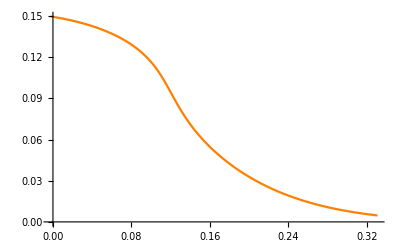

```mathematica
ListPlot[HCcurve,Joined->True, PlotStyle->Orange]
```